# The construction and use of LISA sensitivity curves https://arxiv.org/abs/1803.01944

Hint: using LogLogPlot to plot the figure!!

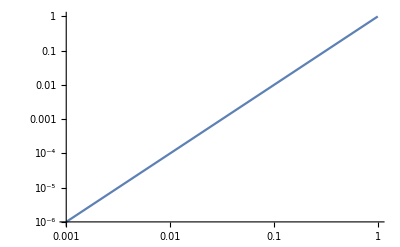

```mathematica
LogLogPlot[x^2,{x,10^-3,1}]
```

## Sensitivity Curves Note: L=2.5*10^9 m, f_*=19.09*10^-3 Hz

## Task01: using eq.(10) to write P_OMS(f) function and plot it.

```mathematica
mHz=10^-3;
```

```mathematica
Subscript[P, OMS][f_]:=(1.5*10^-11)^2*(1+((2*mHz)/f)^4)
```

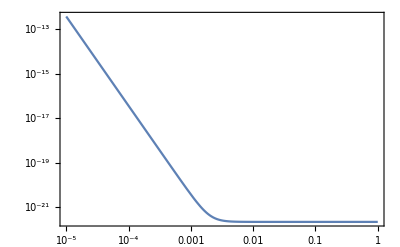

```mathematica
LogLogPlot[Subscript[P, OMS][f],{f,10^-5,1},Frame->True]
```

## Task02: using eq.(11) to write P_acc(f) function and plot it.

```mathematica
Subscript[P, acc][f_]:=(3*10^-15)^2*(1+((0.4*mHz)/f)^2)*(1+(f/(8*mHz))^4)
```

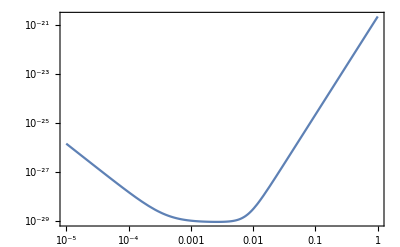

```mathematica
LogLogPlot[Subscript[P, acc][f],{f,10^-5,1},Frame->True]
```

## Task03:using eq.(12) to write P_n(f) function and plot it.

```mathematica
L=2.5*10^9;
fStar=19.09*10^-3;
```

```mathematica
Subscript[P, n][f_]:=(Subscript[P, OMS][f])/L^2+2*(1+Cos[f/fStar]^2)*(Subscript[P, acc][f])/((2*π*f)^4*L^2)
```

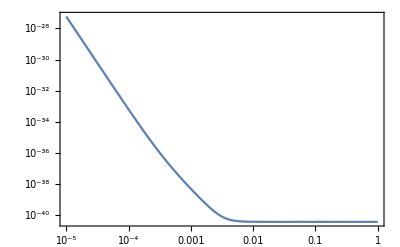

```mathematica
LogLogPlot[Subscript[P, n][f],{f,10^-5,1},Frame->True]
```

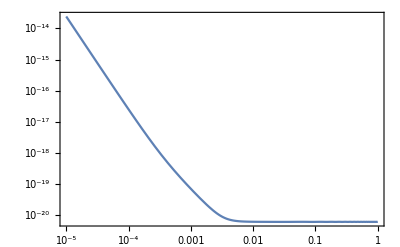

```mathematica
LogLogPlot[(Subscript[P, n][f])^(1/2),{f,10^-5,1},Frame->True]
```

## Task04:using eq.(14) to write S_c(f) function and plot it. Note: choose observation time to be 4 years.

```mathematica
α=0.138;
β=-221;
κ=521;
γ=1680;
fκ=0.00113;
A=9*10^-45;
```

```mathematica
Subscript[S, c][f_]:=A*f^(-7/3)*ⅇ^(-f^α+β*f*Sin[κ*f])*(1+Tanh[γ*(fκ-f)])
```

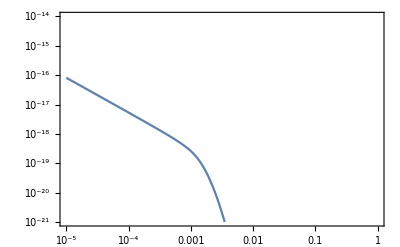

```mathematica
LogLogPlot[(Subscript[S, c][f])^(1/2),{f,10^-5,1},Frame->True,PlotRange->{{10^-5,1},{10^-21,10^-14}}]
```

## Task05:using eq.(1) to write S_n(f) function and plot it.

```mathematica
Subscript[S, n][f_]:=10/(3*L^2)*(Subscript[P, OMS][f]+(4*Subscript[P, acc][f])/(2*π*f)^4)*(1+6/10*(f/fStar)^2)+Subscript[S, c][f];
```

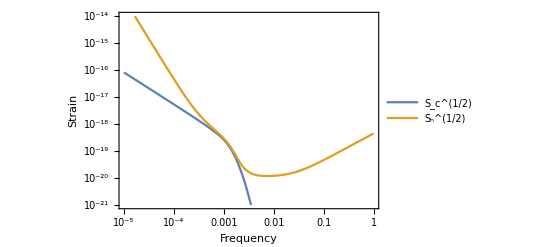

```mathematica
LogLogPlot[{(Subscript[S, c][f])^(1/2),(Subscript[S, n][f])^(1/2)},{f,10^-5,1},Frame->True,FrameLabel->{"Frequency","Strain"},PlotRange->{{10^-5,10^0},{10^-21,10^-14}},PlotLegends->{"S_c^(1/2)","S_n^(1/2)"}]
```

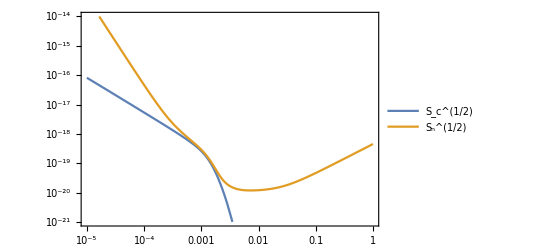

```mathematica
LogLogPlot[{(Subscript[S, c][f])^(1/2),(Subscript[S, n][f])^(1/2)},{f,10^-5,1},Frame->True,PlotRange->{{10^-5,1},{10^-21,10^-14}},PlotLegends->{"S_c^(1/2)","S_n^(1/2)"}]
```

## Binary Sources

## Task06:using eq.(21) to write f_k(m_1, m_2) functions with k=(0, 1, 2, 3).

```mathematica
ak[0]=2.9740*10^-1;
ak[1]=5.9411*10^-1;
ak[2]=5.0801*10^-1;
ak[3]=8.4845*10^-1;
```

```mathematica
bk[0]=4.4810*10^-2;
bk[1]=8.9794*10^-2;
bk[2]=7.7515*10^-2;
bk[3]=1.2848*10^-1;
```

```mathematica
ck[0]=9.5560*10^-2;
ck[1]=1.9111*10^-1;
ck[2]=2.2369*10^-2;
ck[3]=2.7299*10^-1;
```

```mathematica
G=6.67430*10^-11;
lC=2.99792458*10^8;
MSun=1.989×10^30;
```

```mathematica
M[m1_,m2_]:=(m1+m2)*MSun;
η[m1_,m2_]:=(m1*m2)*MSun^2/M[m1,m2];
```

```mathematica
fk[m1_,m2_,k_]:=(ak[k]*η[m1,m2]^2+bk[k]*η[m1,m2]+ck[k])/(π*(G*M[m1,m2]/lC^3))
```

## Task07:using eq.(23) to write ω(m_1, m_2) function.

```mathematica
ω[m1_,m2_]:=(π*fk[m1,m2,2])/2*(fk[m1,m2,0]/fk[m1,m2,1]);
```

## Task08:using eq.(22) to write ℒ(f, f_1, f_2) function.

```mathematica
ℒ[f_,f1_,f2_]:=1/(2*π)*f2/((f-f1)^2+f2^2/4)
```

## Task09:using eq.(20) to write A(f, m_1, m_2, D_L) function.

```mathematica
Mpc=3.08567758×10^16*10^6;
```

```mathematica
ℳ[m1_,m2_]:=(m1*MSun*m2*MSun)^(3/5)/M[m1,m2]^(1/5)
```

```mathematica
AA[f_,m1_,m2_,DL_]:=√(5/24)*((G*ℳ[m1,m2]/lC^3)^(5/6)*fk[m1,m2,0]^(-7/6))/(π^(2/3)*(DL*Mpc/lC))*Piecewise[{
{(f/fk[m1,m2,0])^(-7/6), f<fk[m1,m2,0]},
{(f/fk[m1,m2,0])^(-2/3), fk[m1,m2,0]≤f<fk[m1,m2,1]},
{ω[m1,m2]*ℒ[f,fk[m1,m2,1],fk[m1,m2,2]], fk[m1,m2,1]≤f<fk[m1,m2,3]}
}]
```

## Task10:using eqs. (1.1), (1.2) and (1.3) of https://arxiv.org/pdf/1111.6396 to write D_L(z) function. We set C = 2.99792458*10^8 m/s Ω_m=0.286 H0=69.6 km/s/Mpc 1Mpc = 3.08567758 × 10^16*10^6m

## Task11:using eq.(19) to write S_h(f, m_1, m_2, z) function.

## Task12:using eq.(18) to averaged SNR for a binary source with m_1=m_2=10^6 M_sunand z=3.

## Errors

```mathematica
test[x_]:=x^2
```

## type 1

```mathematica
(x+1)*test(x)
```

test x (1+x)

```mathematica
(x+1)*test[x]
```

x^2 (1+x)

## type 2

```mathematica
(x+1)*[test[x]+y]
```

```mathematica
(x+1)*(test[x]+y)
```

(1+x) (x^2+y)

## type 3

```mathematica
a=3,b=4
```

```mathematica
a=3;b=4
```

4

## type 4

```mathematica
Y=3
Y[x_]:=x^2
```

3

SetDelayed::write: Tag Integer in 3[x_] is Protected.

$Failed